```mathematica
expData=Import["/mnt/heimdall/TwoDim/twoWellSym/T0p15-twoWellSym-Tubes/2WellSymTubes-T0.15-pos0000500.dat","Table"];
```

```mathematica
Dimensions[expData]
```

{20001,16}

```mathematica
data[i_]:=Flatten[Transpose[expData][[i]]][[1000;;19000]]
```

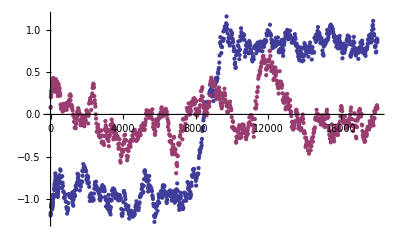

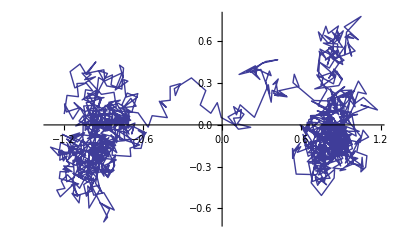

```mathematica
ListPlot[{data[1],data[2]},MaxPlotPoints->1000]
ListLinePlot[Transpose[{data[1],data[2]}],MaxPlotPoints->1000]
```

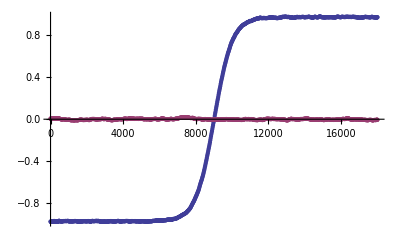

```mathematica
ListPlot[{data[3],data[4]},MaxPlotPoints->1000]
```

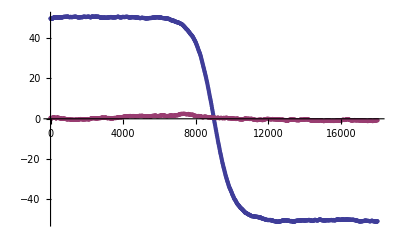

```mathematica
ListPlot[{data[5],data[6]},MaxPlotPoints->1000]
```

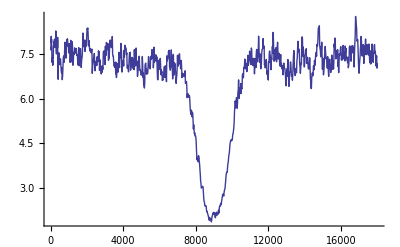

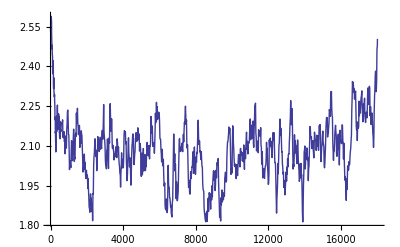

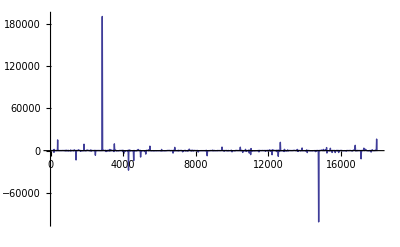

```mathematica
ListLinePlot[0.15/(data[7]-data[3]*data[3]),MaxPlotPoints->1000,PlotRange->All]
ListLinePlot[0.15/(data[8]-data[4]*data[4]),MaxPlotPoints->1000,PlotRange->All]
ListLinePlot[0.15/(data[9]-data[3]*data[4]),MaxPlotPoints->1000,PlotRange->All]
```

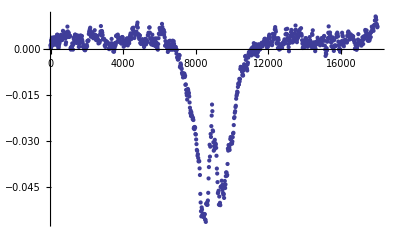

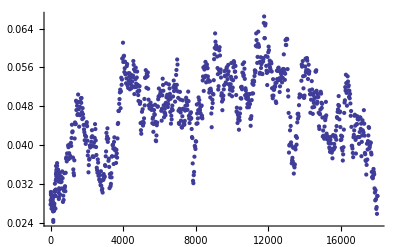

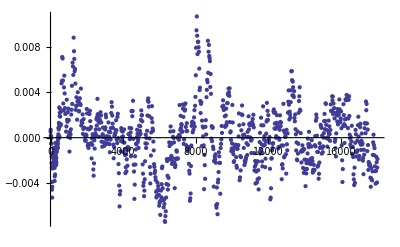

```mathematica
ListPlot[data[10]-data[13]*data[16],MaxPlotPoints->1000,PlotRange->All]
ListPlot[data[11]-data[14]*data[16],MaxPlotPoints->1000,PlotRange->All]
ListPlot[data[12]-data[15]*data[16],MaxPlotPoints->1000,PlotRange->All]
```